```mathematica
NotebookInformation[]
```

{FileName→FrontEnd`FileName[{$RootDirectory,Users,ccarter,Projects_Local,dmse_git_hub,3029,development-material,Craigs_Development_Materials,Polymers},Random_Motion_Of_Polymer.nb,CharacterEncoding→UTF-8],FileModificationTime→3.85472×10^9,WindowTitle→Random_Motion_Of_Polymer.nb,MemoryModificationTime→3.85472×10^9,ModifiedInMemory→True,StorageSystem→Local,DocumentType→Notebook,MIMEType→application/vnd.wolfram.nb,StyleDefinitions→{FrontEndObject[LinkObject["i8kkj_shm", 3, 1]]4},ExpressionUUID→f221cdb3-a6df-4334-a826-7b43085048b4}

## Geometry in the frame where the blue particle moves along the x-axis:

### -Graphics-

### Equation for the position of the orange particle

```mathematica
{Δx2[s],Δy2[s]}={Δx1[s],0}  + {Cos[β[s]],Sin[β[s]]}
```

```mathematica
Cos[β[s] - Pi/2]
```

#### Let’s suppose that the rate of change of the angle β is proportional to the force projected in the radial direction of motion. ν is a “stickiness” coefficient. When ν=1, it will be rigid motion.

```mathematica
eq =D[β[s],s]== (1-ν) Sin[β[s]]
```

#### Let the initial angle be β_0

```mathematica
DSolve[  {eq,β[0]==β0},β[s],s]
```

```mathematica
β[s_,ν_,β0_]:= 2 ArcCot[ⅇ^(-s+s ν) Cot[β0/2]]
```

#### Use Rotation Transform to make the initial direction of the blue particle correspond with θ

```mathematica
DynamicModule[{p1,p2,p0},
Manipulate[
p1 = RotationTransform[θ][{s,0}];
p2 = RotationTransform[θ][{s,0} + AngleVector[β[s,ν,β0-θ]]];
Graphics[
{Blue,Circle[p1,1/2],
Orange,
Circle[p2,1/2]},
PlotRange->8{{-1,1},{-1,1}},Frame->True],
{s,0,5},
{θ,0, 2Pi},
{ν,0,1},
{β0,-Pi,Pi}
]
]
```

#### Example of 5 particles being dragged by particle #3

Note, the angles go like this: β21, β32,β33,β34,β45
The order of the angles changes.
The particles to the left of particle 3 have decreasing indices; the particles to the right have increasing indices.

```mathematica
DynamicModule[{d1,d2,d3,d4,d5, β33 =0},Manipulate[
Graphics[
d3 = s AngleVector[β[s,ν,β33]];
d4 = d3 + AngleVector[β[s,ν,β34-θ]];
d5 = d4 + AngleVector[β[s,ν,β45-θ]];
d2 = d3 + AngleVector[β[s,ν,β32-θ]];
d1 = d2 + AngleVector[β[s,ν,β21-θ]];

{Blue,
Circle[RotationMatrix[θ].d3,1/2],
Orange,
Circle[RotationMatrix[θ].d4,1/2],
Circle[RotationMatrix[θ].d5,1/2],
Circle[RotationMatrix[θ].d2,1/2],
Circle[RotationMatrix[θ].d1,1/2](*,
Line[{{0,0},1AngleVector[θ]}],
Blue,Orange,
Line[{RotationMatrix[θ].AngleVector[β[0,ν,β0-θ] ],RotationMatrix[θ].({s,0}+AngleVector[β[s,ν,β0-θ]])}]*)
,Black,
Text[1,RotationMatrix[θ].d1],
Text[2,RotationMatrix[θ].d2],
Text[3,RotationMatrix[θ].d3],
Text[4,RotationMatrix[θ].d4],
Text[5,RotationMatrix[θ].d5]


},
PlotRange->3{{-1,1},{-1,1}},Frame->True
],
{s,0,1},
{θ,0, 2Pi},
{ν,0,1},
{β45,-Pi,Pi},
{{β34,Pi/2},-Pi,Pi},
{{β32,-1},-Pi,Pi},
{{β21,-1},-Pi,Pi}
]
]
```

#### Illustration of the propagation of disturbance behavior of the subsequent points.

```mathematica
Clear[s,ν,θ];β33=0;
d3 = s AngleVector[β[s,ν,β33]];
d4 = d3 + AngleVector[β[s,ν,β34-θ]];
d5 = d4 + AngleVector[β[s,ν,β45-θ]];
d2 = d3 + AngleVector[β[s,ν,β32-θ]];
d1 = d2 + AngleVector[β[s,ν,β21-θ]];
RotationTransform[θ][{d1,d2,d3,d4,d5}]//FullSimplify//Grid
```

#### Note the recursive behavior of the terms as they propagate from the preceding link in the chain until they reach the particle that was set in motion (above, that particle was 3). Each term is the sum of its predecessor by sines and cosines of an “reduced” angle: We can precompute all of these reduced angles efficiently and then use a recursive definition to compute the displacements

```mathematica
precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]
```

For example:

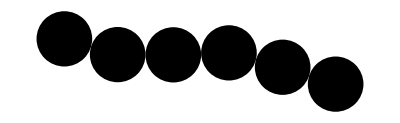

```mathematica
positions = AnglePath[RandomReal[{-.3,.3},5]];
Graphics[Disk[#,1/2]&/@positions]
```

```mathematica
Grid[precompute[positions,3,s,ν,θ],Frame->All]
```

Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (2.85259-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (2.85259-θ)]]]
Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (3.1373-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (3.1373-θ)]]]
Cos[θ] | Sin[θ]
Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (0.0357436-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (0.0357436-θ)]]]
Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-0.263076-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-0.263076-θ)]]]
Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-0.310738-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-0.310738-θ)]]]

#### Here is the displacement function. It creates a recursive function each time it is called, and then uses recursion to compute each displacement, and memoizes (i.e., remembers) each computation.

```mathematica
displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
newPositions[index_] := newPositions[index]=
Which[
index> perturbedIndex,newPositions[index-1] + Δ[[index]],
True,newPositions[index+1] + Δ[[index]]];
newPositions/@Range[Length[Δ]]
]
```

Note: This function doesn’t check for collisions. We will fix that up later.

#### For example:

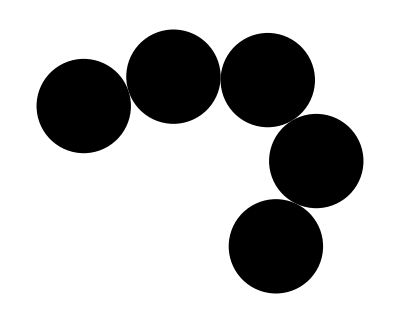

```mathematica
positions = AnglePath[RandomReal[{-1,1},4]];
Graphics[Disk[#,1/2]&/@positions]
```

```mathematica
displacements[2,positions,s,ν,θ]//Short
displacements[2,positions,.1,.1,Pi/3]
```

{{0.950369+s Cos[θ]+Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-«18»-θ)]]],«1»},«4»}

{{0.0696593,0.0319687},{1.00037,0.397726},{1.9935,0.280687},{2.43965,-0.614269},{2.00563,-1.51517}}

#### Visualization:

```mathematica
chainGraphic[positions_]:= 
{FaceForm[Orange],EdgeForm[Black],Disk[#,1/2]&/@(positions),
MapIndexed[Text[#2[[1]],#1]&,(positions)]}
```

```mathematica
DynamicModule[
{positions = AnglePath[RandomReal[{-1,1},8]]},
Manipulate[
If[reset,positions = AnglePath[RandomReal[{-1,1},8]];reset=False];
Graphics[
{ chainGraphic[displacements[i,positions,s,0,θ]],
{Red,PointSize[0.01],Point[positions[[i]]],Arrow[{positions[[i]],positions[[i]]+6 AngleVector[θ]}]}},
PlotRange->p{{-1,1},{-1,1}},Frame->True
],
{{s,0,Style["Displacement",14]},0,3},
{{θ,Pi/2,Style["Displacement Direction",14]},-Pi, Pi},
{{i,1,Style["Particle to Displace",14]},Range[Length[positions]]},
{{p,10,Style["Zoom",14]},2,20},
Delimiter,
{{reset,False,Style["Reset Initial Configuration",14]},{True,False}}
]
]
```

#### Using the visualization tool, you will see that the chain will occasionally “intersect” itself. This is because we have not included a collision detection algorithm yet. We will do that below. But, first let’s use our current model to illustrate how we will implement Brownian motion of a polymer.

### Random Motion

#### We will model the motion of an isolated particle by assuming that a temperature bath applies a random force to a randomly chosen atom in the chain.

```mathematica
positions = AnglePath[RandomReal[{-0.5,0.5},12]];
currentGraphic = Graphics[chainGraphic[positions],PlotRange->15{{-1,1},{-1,1}},Frame->True];
Dynamic[currentGraphic]
```

```mathematica
With[{stiffness = 0.1, relativeTemperature = 0.1},
Do[
With[{whichParticle =RandomInteger[{1,Length[positions]}],
perturbation = RandomVariate[MaxwellDistribution[relativeTemperature]],
angle = RandomReal[2Pi]
},
(*positions =(Mean[positions]+#)&/@displacements[whichParticle,positions,perturbation,stiffness,angle];*)positions=displacements[whichParticle,positions,perturbation,stiffness,angle];
currentGraphic = Graphics[chainGraphic[positions],PlotRange->15{{-1,1},{-1,1}},Frame->True];
];Pause[0.05],
{10}
]
]
```

### Collision Detection and Avoidance (in progress)

```mathematica
displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{displacement,betaList,Δ  },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
displacement[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
displacement[index_] := displacement[index]=
Which[
index> perturbedIndex,displacement[index-1] + Δ[[index]],
True,displacement[index+1] + Δ[[index]]];
displacement/@Range[Length[Δ]]
]
```

```mathematica
Pi/6+0.039
```

0.562599

{{0.,0.},{0.844589,0.535416},{1.27125,1.43983},{1.14736,2.43212},{0.511441,3.20388},{-0.438861,3.51521},{-1.40817,3.26935},{-2.09519,2.54271},{-2.2864,1.56116},{-1.92235,0.629785},{-1.1162,0.038069}}

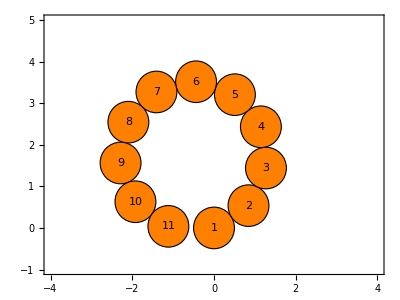

```mathematica
positions = AnglePath[ConstantArray[0.565,10]];
Graphics[chainGraphic[positions],PlotRange->{{-4,4},{-1,5}},Frame->True]
```

```mathematica
Union@Flatten[DistanceMatrix[positions]+ IdentityMatrix[Length[positions]]]//N
```

{1.,1.,1.,1.11685,1.92072,1.92072,1.92072,2.02288,2.02288,2.68918,2.68918,2.76855,2.76855,2.76855,3.24444,3.24444,3.24444,3.29473,3.29473,3.29473,3.5425,3.5425,3.5425,3.5425,3.55971,3.55971,3.55971}

One approach would be to limit the magnitude of the perturbation distance so that no  collisions occur. For example:

```mathematica
Manipulate[
Union[Flatten[DistanceMatrix[displacements[11,positions,s,.1,0],PerformanceGoal->"Speed"]+ IdentityMatrix[Length[positions]]]],
{s,0,1}
]
```

This would be fairly easy to code.

Another approach would be to detect collisions in the recursive part in the displacements function.  If a collision is found, then that displacement is limited.

```mathematica
displacementsNew[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{displacement,betaList,Δ , computedPositions,collisionDistance },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
displacement[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
computedPositions = displacement[perturbedIndex];
displacement[index_] := displacement[index]=
Which[
index> perturbedIndex,
Module[{testPoint=displacement[index-1] + Δ[[index]]},
collisionDistance = Nearest[computedPositions][testPoint][[1]];
Which[collisionDistance>= 1, AppendTo[computedPositions,testPoint];testPoint,
True, AppendTo[computedPositions,displacement[index-1]];displacement[index-1]]
],
True,
Module[{testPoint=displacement[index+1] + Δ[[index]]},
collisionDistance = Nearest[computedPositions][testPoint][[1]];
Which[collisionDistance>= 1, AppendTo[computedPositions,testPoint];testPoint,
True, AppendTo[computedPositions,displacement[index+1]];displacement[index+1]]
]
];
displacement/@Range[Length[Δ]]
]
```